## Monte Carlo, Area

```mathematica
$Line=0;
```

Consider  a  circle  (x-2)^2+(y-1)^2=4  and  its  upper  right  quarter ( pie)  with area   π.

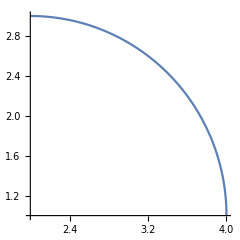

```mathematica
Plot[1+√(4x -x^2),{x,2,4},AspectRatio->1]
```

By the Law of Large Numbers

 (#  pie hits)/n      →     (Area (pie))/(Area(sampled  rectangle [2,4]x[1,3])) = π/4 ,     as   n  →  ∞

This  means      4 (# pie hits)/n  ≈ π    when    n  becomes large.

```mathematica
pie1[n_]:=(hits=0;Do[{x,y}={RandomReal[{2,4}],RandomReal[{1,3}]};If[ (x-2)^2+(y-1)^2≤4,hits=hits+1],{i,1,n}]; 4hits/n//N)
```

```mathematica
Print["π = ",π//N]
Print[ "Monte Carlo approximation = ",pie1[1000000]]
```

π = 3.14159

Monte Carlo approximation = 3.14264

```mathematica
pie2[n_]:=(hitsCount=0;hitsPoints={};Do[{x,y}={RandomReal[{2,4}],RandomReal[{1,3}]};If[(x-2)^2+(y-1)^2≤4,hitsCount=hitsCount+1; hits=AppendTo[hitsPoints,{x,y}]],{i,1,n}];4 hitsCount/n//N)
```

```mathematica
Print["π = ",π//N]
Print[ "Monte Carlo approximation = ",pie2[10000]]
```

π = 3.14159

Monte Carlo approximation = 3.1444

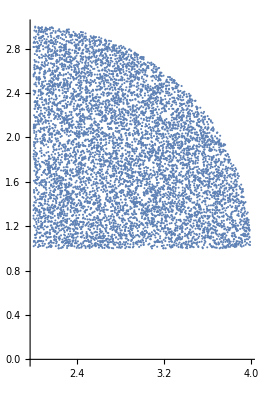

```mathematica
ListPlot[hitsPoints,AspectRatio->Automatic]
```

## Standard Monte Carlo, integration

```mathematica
Clear[x]
```

```mathematica
∫_0^1 ⅇ^(√x)/(3Cos[x])ⅆx
```

∫_0^1 1/3 ⅇ^(√x) Sec[x]ⅆx

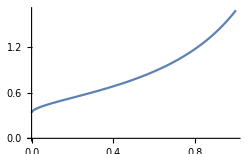

```mathematica
Plot[ⅇ^(√x)/(3Cos[x]),{x,0,1},AxesOrigin->{0,0}]
```

```mathematica
NIntegrate[ⅇ^(√x)/(3Cos[x]),{x,0,1}]
```

0.848372

```mathematica
f[x_]:=ⅇ^(√x)/(3Cos[x])
```

FACT.   ∫_0^1 f(x)ⅆx   can be seen  E f(X)  where X ~ U[0,1], because E f(X) =∫_0^1 f(x)ⅆx.  
              Then by the Law of Large Numbers   (f(X_1) +...+ f(X_n))/n → Ef(X),  where X_1, . . . , X_n  are i.i.d.  ~ X.

```mathematica
s=0;n=100000;
Do[s=s+f[RandomReal[]],{n}]
MonteCarloIntegral=s/n//N
```

0.848262

#### Example1

```mathematica
Clear[f]
```

```mathematica
∫_0^1 4 √(1-x^2) ⅆx
```

π

```mathematica
f[x_]:=4 √(1-x^2)       (* 0 ≤ x ≤ 1 *)
```

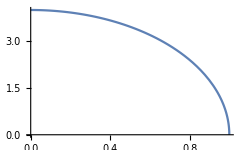

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
s=0; n=1000000;
Do[s=s+f[RandomReal[]],{n}];
a=MonteCarloIntegral=s/n//N;
exact=π//N;
Print["exact = ",exact]
Print["Monte Carlo = ",a]
Print["error = ", Abs[a-exact]]
```

exact = 3.14159

Monte Carlo = 3.1418

error = 0.000206938

## Importance Sampling Monte Carlo, integration

( variance reduction technique )

Suppose we want to estimate the integral  I  = ∫_0^1 f(x)ⅆx.  The Monte Carlo estimator  is based on the following observation
I = E f(U), where  U ~ U[0,1] = uniform distribution on the interval [0,1].  By the Law of Large Numbers 

I_n = 1/n∑_(i=1)^n f(U_i)    →   I  =  Ef(U)  = ∫_0^1 f(x)ⅆx      (*  I_n  is an unbiased estimator of  I  *).

Consider  any probability density  φ(x) > 0  on  [0,1].  Then we have 

I  = ∫_0^1 (f(x))/(φ(x))φ(x)ⅆx  =   E(f(X))/(φ(X)) ,    where  X  follows the  distribution corresponding to the density  φ(x)

Then the Importance Sampling estimator 

J_n = 1/n∑_(i=1)^n (f(X_i))/(φ(X_i)) ,   where  X_i's   are  i.i.d.  ~  φ(x)   

and 

J_n (φ) = 1/n∑_(i=1)^n (f(X_i))/(φ(X_i))     →  ∫_0^1 f(x)ⅆx      (*  J_n  is an unbiased estimator of  I  *)

The key element here is to look  at the variance of J_n (φ) and compare it to the variance of  I_n.  Namely, for    f(x)=4 √(1-x^2)  
with  I  = ∫_0^1 f(x)ⅆx = π  we have

Var(I_n) = 1/n(∫_0^1 f^2(x)ⅆx - I^2)  = 1/n(∫_0^1 16(1-x^2)ⅆx - π^2)  =  1/n (.797) 

Var(J_n(φ)) = 1/n(∫_0^1 ((f(x))/(φ(x)))^2 φ(x)ⅆx - I^2)  = 1/n(∫_0^1 (f(x))^2/(φ(x))ⅆx - I^2)   =  1/n(∫_0^1 (16(1-x^2))/(φ(x))ⅆx - π^2)  

PROBLEM.  Find a function φ(x)  such that  (∫_0^1 (16(1-x^2))/(φ(x))ⅆx - π^2)  is small   (or as small as possible).  

Below we illustrate the procedure  through a concrete example.

Pick   sampling  probability  density  φ ≥0,    φ[x]= a-2(a-1) x    (a linear function), 
   ∫φ[x]ⅆx=1 ~ (proportional) to f[x]. To minimize the variance we chose a=3/2

     Var[J_n(φ)]=1/n[∫_0^1 (16(1-x^2))/φ[x]ⅆx - I^2]=1/n[∫_0^1 (16(1-x^2))/(3/2-x)ⅆx - π^2]=1/n(.158)

     Observe that this is by a factor of 5 better than sampling  uniform ditribution on [0,1] for which variance was 1/n(.797). We need 5 times fewer samples to achieve the same confidence intervals for the value of the integral sought.  Monte Carlo sampling according to φ  cuts the error (standard deviation) by a factor  √variance  =√5=2.23  or better than in half.

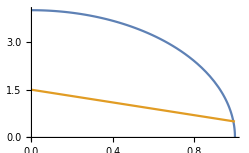

```mathematica
Plot[{f[x],3/2-x},{x,0,1}]
```

To sample  X  according to the density φ[x] we  consider its  distribution function

F[x]=P{X ≤ x } =  ∫_0^x φ[u]ⅆu = ∫_0^x (3/2-u) ⅆu  =3/2 x- 1/2 x^2  , 0 ≤ x  ≤1

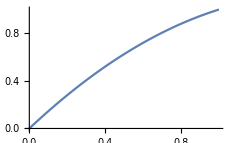

```mathematica
Plot[3/2 x- 1/2 x^2 ,{x,0,1}]
```

and  use the following important piece of information

THEOREM.  Let  F(x) = P ( X ≤ x ) be a strictly increasing distribution function of a random variable X.  Let U  be a random variable 
 with uniform distribution on the interval [0,1].  Define a random variable X=F^-1(U). Then X  has the distribution function F.

A sample {X_i}  with density φ[x] is obtained by generating transformations of uniformly distributed random variables {U_i} on [0, 1].

### Example 2 (Importance Sampling)

```mathematica
f[x_]:=4 √(1-x^2)       (* 0 ≤ x ≤ 1 *)
```

### Standard Monte Carlo

```mathematica
s=0; n=1000000;     (* standard sampling  ~ uniform distribution on [0,1] *)
Do[s=s+f[RandomReal[]],{n}];
a=MonteCarloIntegral=s/n//N;
exact=π//N;
Print["exact = ",exact]
Print["Monte Carlo = ",a]
Print["error = ", Abs[a-exact]]
```

exact = 3.14159

Monte Carlo = 3.14054

error = 0.00105022

### Importance Sampling Monte Carlo

```mathematica
f[x_]:=4 √(1-x^2)       (* 0 ≤ x ≤ 1 *)
```

```mathematica
φ[x_]:=3/2-x;    g[x_]:=f[x]/φ[x];
```

```mathematica
Clear[y]
```

```mathematica
Solve[3/2 x- 1/2 x^2 ==y,x]              (* 0 ≤ x ≤ 1 *)
```

{{x→1/2 (3-√(9-8 y))},{x→1/2 (3+√(9-8 y))}}

Pick the correct inverse 1/2 (3-√(9-8 y)), where  0 ≤ y ≤ 1,  rename y = u  and set

```mathematica
H[u_]:=(3-√(9-8u))/2;      
(* H = F^-1, where F[x]=P(X ≤ x)=3/2 x- 1/2 x^2 = y     0 ≤ x ≤1 where F has density φ *)
```

```mathematica
s=0; n=200000; (* importance sampling ~ density φ[x] on [0,1] *)
Do[s=s+g[H[RandomReal[]]],{n}];
a=MonteCarloIntegral=s/n//N;
exact=π//N;
Print["exact = ",exact]
Print["Monte Carlo = ",a]
Print["error = ", Abs[a-exact]]
```

exact = 3.14159

Monte Carlo = 3.14209

error = 0.000501548

CONCLUSION (Importance Sampling is more efficient!)

Generally achieves better accuracy with a lot fewer trials:  
200,000  (Importance Sampling)  versus  1000,0000  (standard Monte Carlo)

## The Acceptance-Rejection Technique

## FACT. No software package or library can have all possible random number generators! QUESTION : How to generate random samples from any possible probability distribution? REMEDY: The Acceptance-Rejection Technique

Generating Discrete Random Variables

Suppose we have an efficient method for simulating an integer-valued random  variable Y having probability mass function  {q_j, j ≥ 0 }.
In order to simulate an integer-valued  random variable X whose distribution has mass function {p_j, j ≥ 0}, we use the following technique, called
 the rejection method or the acceptance/rejection method.
     
The Method
     
      STEP 1   Simulate the value of Y having probability mass function q_j  [from random generators library]
      STEP 2   Generate a random number U  (U ~ uniform distribution on [0,1])    [basic random generator]
      STEP 3   If U  <  p_Y/(c q_Y)  set  X = Y,  else go to STEP 1
          
Specifically, let c be a constant such that p_j/q_j ≤ c for all j such that p_j > 0.  
REMARK. We must have  c  > 1 except when p_j = q_j for each j, in which case c =1.

In addition, as each iteration independently results in an accepted value with probability 1/c, we see that 
N = number of iterations needed has geometric distribution with expected value E[N] = c. 
     
Example Suppose we want to simulate outcomes of a random variable X that takes values from { 1,2, . . . , 10} with respective probabilities  {0.05,  0.07,  0.10,  0.12,  0.16,  0.15,  0.14,  0.11,  0.06, 0.04} . Rejection method tells us to use Y being the discrete uniform density 
on  1, . . . , 10}.  That is, q_j = 1/10, j =  1, . . . , 10. For this choice of {q_j} we can pick  c = Max {p_j/q_j , j ≥0}=1.6  or   c q_j= .16  and the algorithm goes as follows:

     STEP 1   Generate a random number Y       
     STEP 2   Generate a  random number U
     STEP 3   If U ≤ p_Y/(.16) set X = Y, else go to STEP 1.
          
REMARK.  On average, this algorithm requires  c =1.6 iterations of the above to obtain the generated value of X.

```mathematica
Clear[u,i,p]
p={0.05,0.07,0.10,0.12,0.16,0.15,0.14,0.11,0.06,0.04};
simu1={};
Do[{i=RandomInteger[{1,10}],u=RandomReal[],If[u≤p[[i]]/0.16,AppendTo[simu1,i]]},{10000}]
```

```mathematica
g1=Histogram[simu1,{0.5,10.5,1},"Probability",Ticks->{{0,1,2,3,4,5,6,7,8,9,10},{.025,.05,.075,.1,.125,0.15}}];
g2=Plot[Piecewise[{{0.05,0.5≤x<1.5},{0.07,1.5≤x<2.5},{0.1,2.5≤x<3.5},{0.12,3.5≤x<4.5},{0.16,4.5≤x<5.5},{0.15,5.5≤x<6.5},{0.14,6.5≤x<7.5},{0.11,7.5≤x<8.5},{0.06,8.5≤x<9.5},{0.04,9.5≤x<10.5}}],{x,0,10.5}];
```

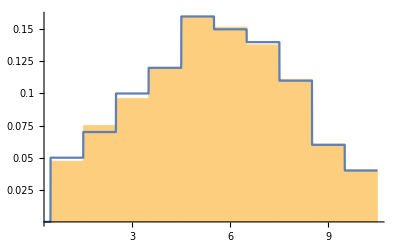

```mathematica
Show [g1,g2]  (* blue is the exact distribution of p, histogram of the simualted data is yellow *)
```

```mathematica
10000/Length[simu1]//N
```

1.59821

```mathematica
(* The above is very close to 1.6 *)
```

To get a sample of 10, 000:

```mathematica
Clear[v,j,t,sam1]
sam1={};t=10000;Label[start];If[Length[sam1]<t,j=RandomInteger[{1,10}];v=RandomReal[];If[v≤p[[j]]/0.16,AppendTo[sam1,j]];Goto[start]]
```

```mathematica
Length[sam1]
```

10000

```mathematica
f1=Histogram[sam1,{0.5,10.5,1},"Probability",Ticks->{{0,1,2,3,4,5,6,7,8,9,10},{.025,.05,.075,.1,.125,0.15}}];
f2=Plot[Piecewise[{{0.05,0.5≤x<1.5},{0.07,1.5≤x<2.5},{0.1,2.5≤x<3.5},{0.12,3.5≤x<4.5},{0.16,4.5≤x<5.5},{0.15,5.5≤x<6.5},{0.14,6.5≤x<7.5},{0.11,7.5≤x<8.5},{0.06,8.5≤x<9.5},{0.04,9.5≤x<10.5}}],{x,0,10.5}];
```

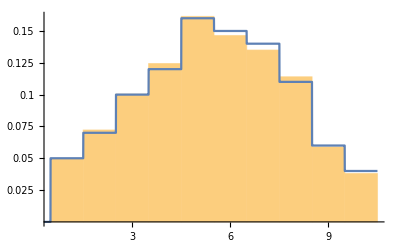

```mathematica
Show[f1,f2]
```

Generating Continuous Random Variables

Suppose we have an efficient method for generating a sample from a continuous random variable Y having density function g(y). Similarly to discrete case, we can use Y as basis for generating values from continuous random variable X  having density function of f(x).
     
 Rejection Method
     
  STEP 1    Generate Y having density g		                [from random generators library]
  STEP 2    Generate a random number U			     [basic random generator]
  STEP 3    If U ≤ (f(Y))/(c g(Y)) set  X = Y, else go to STEP 1
          
 c is a constant such that   (f(Y))/(g(Y)) ≤ c for all y, the number of iterations of the algorithm that are needed has geometric distribution with mean c. 
     
Example. We use the rejection method to generate a random variable having density function f(x) = 4/81 x^3, 0 <  x  < 3. Since this random variable is concentrated in the interval [0,3], let us consider the rejection method with uniform distribution  g(x) = 1/3,  0 <  x  < 3,  that is X ~ U[0,3]

To determine the constant c such that f(x)/g(x) ≤ c, use calculus to find the maximum value of (f(x))/(g(x)) = 12/81 x^3 = 4 = c.
Hence, (f(x))/(c g(x))= 1/27 x^3 and thus the rejection procedure is as follows:

        STEP 1   Generate random number Y                           Y  ~  U[0,3]
        STEP 2   Generate random number U                           U  ~  U[0,1] 
        STEP 3   If U ≤ 1/27 Y^3 set X =  Y , else go to STEP 1

```mathematica
∫_0^3 4/81 x^3 ⅆx
```

1

```mathematica
f[x_]:=4/81 x^3;g[x_]:=1/3;c=4;
```

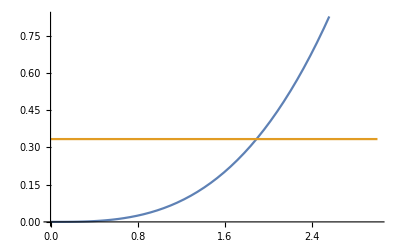

```mathematica
Plot[{f[x],g[x]},{x,0,3}]     (* poor approximation of f(x) by g(x)  *)
```

```mathematica
f[y]/(c g[y])
```

0.351219

```mathematica
simu2={};
Do[y=RandomReal[{0,3}];u=RandomReal[];If[ u≤y^3/27,AppendTo[simu2,y]],{10000}]
```

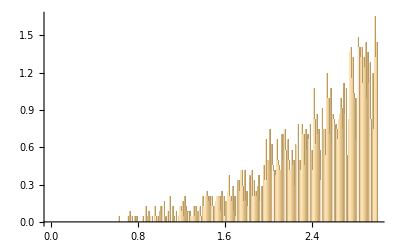

```mathematica
Histogram[simu2,{0,3,0.01},"ProbabilityDensity",ChartElementFunction->"GlassRectangle"]
```

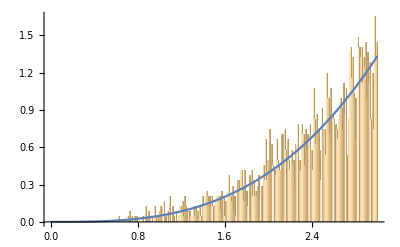

```mathematica
Show[Histogram[simu2,{0,3,0.01},"ProbabilityDensity",ChartElementFunction->"GlassRectangle"],Plot[f[x],{x,0,3}]]
```

```mathematica
10000/Length[simu2]//N       (* exact average = c = 4  *)
```

4.12712

## More efficient g[x] on [0, 3]

```mathematica
Clear[f,g,x]
```

```mathematica
f[x_]:= 4/81 x^3;
g[x_]:=2/9 x;
```

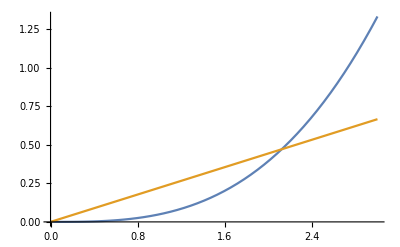

```mathematica
Plot[{f[x],g[x]},{x,0,3}]
```

```mathematica
∫_0^3 f[x]ⅆx
```

1

```mathematica
∫_0^3 g[x]ⅆx
```

1

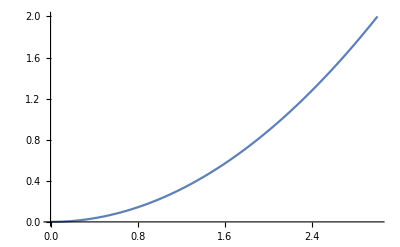

```mathematica
Plot[f[x]/g[x],{x,0,3}]
```

max[f[x]/g[x], 0≤x≤3]=2=c

```mathematica
c=2;   

(* on average it takes 2 steps to get the simulated value accepted or improvemenr from 
g=1/3 with c=4 by a factor of 2 *)

f[x]/(c g[x])
```

x^2/9

```mathematica
Clear[x,u]
```

```mathematica
simu2={};
Do[y=3 √RandomReal[];u=RandomReal[];If[ u≤y^2/9,AppendTo[simu2,y]],{10000}]
```

```mathematica
10000/Length[simu2]//N
```

1.98138

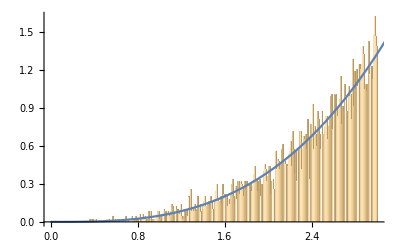

```mathematica
Show[Histogram[simu2,{0,3,0.01},"ProbabilityDensity",ChartElementFunction->"GlassRectangle"],Plot[f[x],{x,0,3.1}]]
```